# Quantum Gas Assembly Movie Making

This Mathematica script was developed to take pictures taken from the Andor camera and turn them into movies.

## Parameters

```mathematica
date="160518";
fitsName = "NoBinningX";
movieName = "XNoBinning";
pixelCountMin = 130;
pixelCountRange = 60;
pictureNumber = 1800;
atomLocation = {2,2};
```

## Import Data

```mathematica
filePath ="\\\\andor\\share\\Data and documents\\Data repository\\"<>date<>"\\"<>fitsName<>".fits";
rawData = Flatten[Import[filePath,"RawData"],1];
horizontalDimension = Dimensions[rawData [[1]]][[1]];
verticalDimension= Dimensions[rawData [[1]]][[2]];
```

## Scale Data

```mathematica
scaledData  = rawData;
Do[Do[Do[scaledData[[picInc,collumnInc,rowInc]] = 1/pixelCountRange(rawData [[picInc,collumnInc, rowInc]] - pixelCountMin),{picInc,1,pictureNumber}],{rowInc,1,verticalDimension}],{collumnInc,1,horizontalDimension}]
```

## Average Data

```mathematica
averagedData = {};
Do[
Do[
Do[
Do[averagedData[[pictureInc, collumnInc,RowInc]] = scaledData[[[pictureInc + experimentInc * 18,collumnInc,RowInc],{}]],
{}],
{}],
{}],
{}]
```

## See Histograms & Statistics

```mathematica
peakData={};
firstShot={};
For[i=1,i≤Length[rawData],i++,AppendTo[peakData,rawData⟦i,atomLocation⟦1⟧,atomLocation⟦2⟧⟧-1/4 (rawData⟦i,1,1⟧+rawData⟦i,horizontalDimension,verticalDimension⟧+rawData⟦i,1,verticalDimension⟧+rawData⟦i,horizontalDimension,1⟧)];AppendTo[firstShot,rawData⟦i,atomLocation⟦1⟧,atomLocation⟦2⟧⟧-1/4 (rawData⟦i,1,1⟧+rawData⟦i,horizontalDimension,verticalDimension⟧+rawData⟦i,1,verticalDimension⟧+rawData⟦i,horizontalDimension,1⟧)];]
```

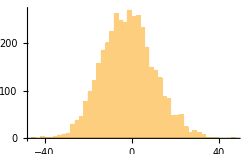

```mathematica
Histogram[firstShot,50, PlotRange-> All, ImageSize-> 250]
```

```mathematica
atomNumber = 0;
For[i = 1, i ≤Length[rawData],i++,
If[firstShot[[i]] > 100, atomNumber++]
];
Print[N[atomNumber/Length[rawData]]]
```

0.

## Convert to Movie & Export

```mathematica
(*movieFrameArray[picNumber_] := ArrayPlot[scaledData[[picNumber]], ColorFunction -> GrayLevel, ColorFunctionScaling->False];*)
movieFrameArray[picNumber_] := ArrayPlot[scaledData[[picNumber]], ColorFunction -> "BlueGreenYellow", ColorFunctionScaling->False];
```

```mathematica
movieData = ParallelTable[movieFrameArray[picNumber],{picNumber, 1, 2000}];
```

```mathematica
(*Export["C:\\Users\\Mark\\Documents\\My Data Analysis\\"<>movieName<>".mov",movieData, "FrameRate" -> 2];*)
Export["C:\\Users\\Mark\\Documents\\My Data Analysis\\"<>movieName<>".mov",movieData, "FrameRate" -> 20];
```